```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
```

```mathematica
Product[Sin[(π k/n)],{k,1,n-1}]
```

2^(1-n) n

```mathematica
Product[Gamma[k/n+1]/(k/n),{k,1,n-1}]//(TraditionalForm[Sqrt[#^2]]&)
```

√((2 π)^(n-1)/n)

```mathematica
ClearAll[Li];
Li[x_]:=Integrate[1/Log[y],{y,2,x}]
Li[20.]//N
```

8.86014

```mathematica
LogIntegral[20.]-LogIntegral[2.]
```

8.86014

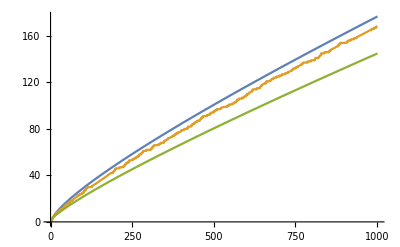

```mathematica
Plot[{LogIntegral[y]-LogIntegral[2],PrimePi[y],y/Log[y]},{y,2,1001},AxesOrigin->{0,0}]
```

```mathematica
D[Log[Log[y]],y]
```

1/(y Log[y])

```mathematica
ClearAll[f];
D[Log[f[x]],x]
```

f'[x]/f[x]

```mathematica
355687428096031./Log[355687428096031]
```

1.06159×10^13

```mathematica
Prime[1061592742441]
```

31909499211529

```mathematica
PrimeQ[31909499211529]
```

True

```mathematica
ClearAll[f];
f[]:=Module[{s1,s2,i},
s1={};
s2={};
i=1;
While[Prime[i]<400,
s1=AppendTo[s1,Prime[i]];
If[PrimeQ[800-Prime[i]],
s2=AppendTo[s2,{Prime[i],800-Prime[i]}]];
i=i+1;];
s2]
f[]
```

{{3,797},{13,787},{31,769},{43,757},{61,739},{67,733},{73,727},{109,691},{127,673},{139,661},{157,643},{181,619},{193,607},{199,601},{223,577},{229,571},{277,523},{313,487},{337,463},{367,433},{379,421}}

# Analytic Number Theory

Arithmetic

## Division

## Greatest Common Divisor

## Prime Numbers

### Prime Gap size n

#### Example

```mathematica
ClearAll[f,g,h,h1,h2]
f[n_]:=Product[Prime[k],{k,1,n}]
g[n_]:=Table[{f[n]+2+k,FactorInteger[f[n]+2+k]},{k,0,n-1}]
h[n_]:=Table[{n!+2+k,FactorInteger[n!+2+k]},{k,0,n-1}]
h1[n_,m_]:=Table[{k+1,n!+2+k,FactorInteger[n!+2+k]},{k,0,m-1}]
h2[n_,m_]:=Select[Table[{k+1,n!+2+k,PrimeQ[n!+2+k]},{k,0,m-1}],#[[3]]==True&]
h2[19,100]//TableForm
FactorInteger[19!+1]
```

88 | 121645100408832089 | True

{{71,1},{1713311273363831,1}}

## Fundamental Theorem of Arithmetic

## Euclidean Algorithm

Tools

## Abel Summation

### Discrete Version

#### Example

```mathematica
ClearAll[a,f,s,A,F];
a[r_]:=r/2
A[n_]:=Sum[a[k],{k,1,n}]
f[r_]:=r+1
F[n_]:=Sum[f[k],{k,1,n}]
s[n_]:=Sum[a[k]f[k],{k,1,n}]
Table[s[k],{k,1,7}]//tf
```

```mathematica
{{1}, {4}, {10}, {20}, {35}, {56}, {84}}
```

{1,4,10,20,35,56,84}

```mathematica
(*
	NOTE: 
	A[0]f[0] zou eigenlijk A[1]f[1] moeten zijn;
	 Pas aan zodat het ook werkt met m;
	 Verder bestuderen Discrete Abel Summation
*)
ClearAll[tmp];
tmp[n_]:=Sum[A[k](f[k]-f[k+1]),{k,1,n-1}]+A[n]f[n]-A[0]f[0]
Table[tmp[k],{k,1,7}]
tmp[7]
```

{1,4,10,20,35,56,84}

84

Arithmetic Functions and Dirichlet Series

### Multiplicative Functions

#### Example

The Prime Number Theorem

Dirichlet’s Theorem

Error Estimates and the Riemann Hypothesis

Temp

## Tmp-1